```mathematica
file4=<<"/Users/ruppell/Math/temp/output-cpx-joined-edm_clean.txt";
```

```mathematica
Dimensions@file4
```

{3312,10}

```mathematica
higgs1[ind_]:=file4[[ind,4,9,2]];
higgs2[ind_]:=file4[[ind,4,9,3]];
tβ[ind_]:=file4[[ind,2,8]];
κ[ind_]:=file4[[ind,2,23]];
λ[ind_]:=file4[[ind,2,21]];
vev1[ind_]:=Sqrt[174^2/(1 +(file4[[ind,2,8]])^2)];
vev2 [ind_]:= vev1@ind*file4[[ind,2,8]];
ϕ2[ind_]:=file4[[ind,2,25]];
ϕS[ind_]:=file4[[ind,2,24]];
vS[ind_]:=file4[[ind,2,10]];
Aκ[ind_]:=file4[[ind,2,28]];
Aλ[ind_]:=file4[[ind,2,27]];
```

```mathematica
higgs1[1]
```

{-0.00448436,-0.0487244,0.0571187,-0.0169928,0.00337923,0.997017}

```mathematica
NeutralScalars[[scalarsN]]
```

{h1,h2,sR,ih1,ih2,sI}

```mathematica
Γijk=Outer[D[Vv,#1,#2,#3]&,
NeutralScalars[[scalarsN]],
NeutralScalars[[scalarsN]],
NeutralScalars[[scalarsN]]]/.allVEV;
```

```mathematica
vertex=Γijk.higgs1[#].higgs1[#].higgs2[#]&;
```

```mathematica
TeV=10^3;GeV=1;MeV=10^-3;
(* Shorthand notations for energy units, these can be changed if we want, e.g., GeV == 1 *)
vSq=(174GeV)^2;
vSqHiggs = vSq;
mW=80.403GeV;
mZ=91.1876GeV;
αew=1/127.908957;θw=ArcSin[Sqrt[0.23124]];mtPole=180GeV;
αstrong=0.102;
mup=1.5MeV;
mcharm=1.1GeV;mtop=mtPole/(1+4*αstrong/(3 Pi));
mdown=3MeV;
mstrange=60MeV;
mbottom=4.1GeV;
melectron=0.511MeV;
mmuon=105.66MeV;
mtau=1.777GeV;
Ytop=mtop /v2;
Ybtm=mbottom /v1;
Ytau=mtau /v1;
g1 := Sqrt[(2*Tan[θw]^2*mW^2)/vSq];
g2 := mW*Sqrt[2/vSq];
GF=1.16637*10^-5 GeV^-2 ;
BRτνν=0.1784;
hc=1.239841857*10^-4*10^-9;
```

```mathematica
Sqrt[αew 4Pi]/(2Sin[θw]Cos[θw])
```

0.371704

```mathematica
V=vertex[#]/.{tanβ->tβ[#],kappa->κ[#],lambda->λ[#],v1->vev1[#],v2->vev2[#],phi2->ϕ2[#],phiS->ϕS[#],vevS->vS[#],Akappa->Aκ[#],Alambda->Aλ[#]}&;
```

```mathematica
Vlist=Abs@Chop@(V/@Range@First@Dimensions@file4);
```

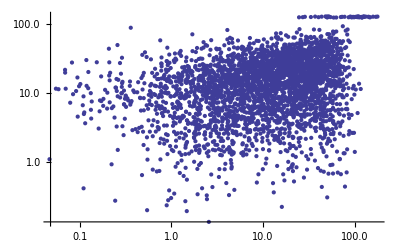

```mathematica
ListLogLogPlot@Transpose@{Vlist,file4[[;;,3,6,2]]}
```

```mathematica
Vpos=Flatten@Position[Vlist,k_/;k<1];
```

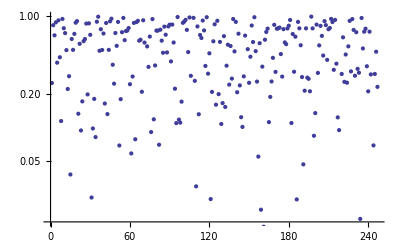

```mathematica
ListLogPlot@Vlist[[Vpos]]
```

```mathematica
file10=file4[[Vpos]];
```

```mathematica
Dimensions@file10
```

{247,10}

```mathematica
snuLSP[name_]:=Select[name,#[[3,5,1]]<Abs@#[[3,1,1]]&];
χ0LSP[name_]:=Select[name,#[[3,5,1]]>Abs@#[[3,1,1]]&];
χ0sing[name_]:=Select[name,Power[Abs@(#[[4,1,1,5]]+I #[[4,1,2,5]]),2]>0.1&];
χ0doub[name_]:=Select[name,Power[Abs@(#[[4,1,1,5]]+I #[[4,1,2,5]]),2]<0.1&];
snuLeft[name_]:=Select[name,#[[4,10,1,4]]^2+#[[4,10,1,8]]^2<0.99&];
snuRight[name_]:=Select[name,#[[4,10,1,4]]^2+#[[4,10,1,8]]^2>0.99&];
selSnuMass[down_,up_][name_]:=Select[name,(#[[3,5,1]]<up&&#[[3,5,1]]>down)&];
selHiggsMass[down_,up_][name_]:=Select[name,Or@@((#<up&&#>down)&/@#[[3,6,{2,3,4,5,6}]])&];
```

```mathematica
bsg[name_]:=Select[name,(#[[9,1]]<4.97*^-4&&#[[9,1]]>2.13*^-4)&];
ΔMd[name_]:=Select[name,(#[[9,2]]<5.15*^-1&&#[[9,2]]>4.99*^-1)&];
ΔMs[name_]:=Select[name,(#[[9,3]]<1.753*^1&&#[[9,3]]>1.801*^1)&];
bsμμ[name_]:=Select[name,(#[[9,4]]<1.1*^-8)&];
bτν[name_]:=Select[name,(#[[9,5]]<2.45*^-4&&#[[9,5]]>8.9*^-5)&];
```

```mathematica
dϵ[name_]:=Select[name,(#[[10,2,1]]<1.43*^-27&&#[[10,2,1]]>-0.5*^-28)&];
dμ[name_]:=Select[name,(#[[10,2,2]]<0.8*^-19)&];
BRτμγ[name_]:=Select[name,(#[[10,3,1]]<4.4*^-8)&];
BRτϵγ[name_]:=Select[name,(#[[10,3,2]]<3.3*^-8)&];
BRμϵγ[name_]:=Select[name,(#[[10,3,3]]<1.2*^-11)&];
```

```mathematica
pName={"M1","M2","M3","M0","Mtau","MQ","MNR","tanβ","v","vevS","Atop","Abtm","Atau","An11","An12","An13","AlambdaN","Yn11","Yn12","Yn13","lambda","lambdaN","kappa","PhisPI","Phi2PI","ksi","Alambda","Akappa","mh1","mh2","mS"};
```

```mathematica
cuts=BRμϵγ@BRτϵγ@BRτμγ@dμ@dϵ@bτν@bsμμ@bsg@#&;
h1[name_]:=Select[name,(#[[3,6,2]]<128&&#[[3,6,2]]>123)&];
h23[name_]:=Select[name,((#[[3,6,3]]<128&&#[[3,6,3]]>123)||(#[[3,6,4]]<128&&#[[3,6,4]]>123))&];
h123[name_]:=Select[name,((#[[3,6,2]]<128&&#[[3,6,2]]>123)||(#[[3,6,3]]<128&&#[[3,6,3]]>123)||(#[[3,6,4]]<128&&#[[3,6,4]]>123))&];
dm[name_]:=Select[name,(#[[6,1]]<0.1311&&#[[6,1]]>0.0941)&];
dmup[limU_,limD_][name_]:=Select[name,(#[[6,1]]<limU&&#[[6,1]]>limD)&];
```

```mathematica
Dimensions@dmup[0.1311,0.]@dϵ@bsg@BRμϵγ@file10
```

{6,10}

```mathematica
{pName[[{4,7,8,10,17,21,22,23,24,25,26,27,28,29,30,31}]]}~Join~(dmup[0.13,0.]@cuts@file10)[[;;,2,{4,7,8,10,17,21,22,23,24,25,26,27,28,29,30,31}]]//TableForm
```

M0 | MNR | tanβ | vevS | AlambdaN | lambda | lambdaN | kappa | PhisPI | Phi2PI | ksi | Alambda | Akappa | mh1 | mh2 | mS
307.121 | 447.708 | 45.7354 | 4277.17 | 337.037 | 0.114356 | 0.720559 | 0.0377641 | 3.22791 | 0.110629 | 118.117 | -51.5866 | -0.81591 | 2132.65 | 0.+458.99 ⅈ | 0.+228.719 ⅈ
320.306 | 207.55 | 43.4645 | 1881.92 | -135.489 | 0.259061 | 0.0346405 | 0.173518 | 3.19899 | 0.141537 | 109.832 | 43.7333 | -0.676945 | 2411.16 | 0.+456.297 ⅈ | 0.+463.418 ⅈ
431.96 | 494.728 | 33.9392 | 964.843 | -668.886 | 0.362511 | 0.0316817 | 0.230804 | 3.14226 | 0.00991259 | 522.907 | 180.337 | -217.475 | 636.489 | 0.+309.187 ⅈ | 0.+57.5486 ⅈ
431.939 | 401.058 | 26.9465 | 914.822 | 319.654 | 0.347335 | 0.497515 | 0.294481 | 3.20331 | 0.249036 | 318.907 | 109.857 | -43.221 | 1143.45 | 0.+269.681 ⅈ | 0.+353.099 ⅈ
472.656 | 341.464 | 30.1326 | 487.454 | 365.302 | 0.429633 | 0.268887 | 0.357058 | 3.21293 | 3.03663 | 253.004 | 1268.25 | -60.9999 | 2629.86 | 0.+99.4355 ⅈ | 0.+206.367 ⅈ
377.028 | 135.736 | 44.92 | 816.713 | -975.542 | 0.340659 | 0.750284 | 0.29215 | 3.17271 | 0.172967 | 300.581 | 129.599 | -45.5142 | 1161.16 | 0.+224.56 ⅈ | 0.+307.986 ⅈ

```mathematica
{{"Spectrum","gHZZ","RD","Channels","DM -- Nucleon", "bsgamma et al", "edm et al"}}~Join~(dmup[0.13,0.]@cuts@file10)[[;;,{3,5,6,7,8,9,10}]]//TableForm
```

Spectrum | gHZZ | RD | Channels | DM -- Nucleon | bsgamma et al | edm et al
296.349 | -322.222 | 471.279 | -494.554 | 626.123 |  |  | 
469.197 | 626.068 |  |  |  |  |  | 
0 | 2178.75 |  |  |  |  |  | 
0 | 2.848×10^-12 | 1.3133×10^-11 | -6163.91 |  |  |  | 
300.239 | 300.239 | 300.239 | 300.239 | 300.239 | 300.239 | 6086.9 | 6272.01
0.0000305176 | 2.74864 | 127.399 | 330.14 | 2174.95 | 2175.01 |  | 
303.296 | 310.252 | 310.252 | 310.758 | 310.758 | 317.56 |  | 
998.553 | 999.356 |  |  |  |  |  | 
1000.32 | 1001.77 |  |  |  |  |  | 
812.027 | 1181.68 |  |  |  |  |  | 
959.033 | 1041.38 |  |  |  |  |  |  | 0.0121772 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
5.05221×10^-6 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0.9438 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0.0440114 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
4.79388×10^-7 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
5.4374×10^-6 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-2.73337×10^-6 | -5.69586×10^-6 | 1.55182×10^-6 | -0.000471197 | -0.0023701 | -1.07594×10^-7 | 1.89669×10^-6 | 0.00107281 | -0.00040466 | 3.89129×10^-6 | 0.0022541 | -0.000749946 | -0.000936033 | -0.00141488 | -0.999992 | 0.0620619
~o1
27.3409 | 0.000031 | ~n1 ~n1 | s S
0.0543 | ~n1 ~n1 | b B
0.00381 | ~n1 ~n1 | c C
0.0087 | ~n1 ~n1 | e2 E2
3.12 | ~n1 ~n1 | e3 E3
0.000645 | ~n1 ~n1 | h1 h1
67 | ~n1 ~n1 | h2 h2
0 | ~n1 ~n1 | n4 n4
0 | ~n1 ~n1 | N4 N4
558 | ~n1 ~n1 | W+ W-
490 | ~n1 ~n1 | Z Z
2.4 | ~o1 ~o1 | b B
0.000053 | ~o1 ~o1 | h1 h1
0.212 | ~o1 ~o1 | h2 h2
40.9 | ~o1 ~o1 | W+ W-
2.34 | ~o1 ~o1 | Z Z | 1.319×10^-9 | 1.319×10^-9 | -6.45342×10^-8 | -6.45342×10^-8
1.31922×10^-9 | 1.31922×10^-9 | 6.28713×10^-8 | 6.28713×10^-8
7.5571×10^-10 | 7.5571×10^-10 | 5.42709×10^-6 | 5.42709×10^-6
7.5596×10^-10 | 7.5596×10^-10 | 5.15102×10^-6 | 5.15102×10^-6 | 0.000455751
0.595112
20.6187
4.17604×10^-9
0.000126862
3.1967×10^-9 | 5.13364×10^-16 | 2.19485×10^-11 | -2.25072×10^-8
7.15338×10^-28 | 1.47911×10^-25 | -1.6438×10^-22
9.45616×10^-21 | 8.09484×10^-21 | 1.17161×10^-19
296.361 | 470.517 | -486.282 | 625.897 | -659.756 |  |  | 
467.895 | 625.803 |  |  |  |  |  | 
0 | 2452.78 |  |  |  |  |  | 
0 | 3.932×10^-12 | 6.96329×10^-10 | -130.382 |  |  |  | 
5.70507 | 313.714 | 313.714 | 313.714 | 313.714 | 313.714 | 313.714 | 346.583
0.0000305176 | 2.4582 | 126.269 | 657.073 | 2449.98 | 2450.03 |  | 
316.64 | 323.308 | 323.308 | 323.794 | 323.794 | 330.327 |  | 
998.553 | 999.356 |  |  |  |  |  | 
1000.32 | 1001.77 |  |  |  |  |  | 
811.989 | 1181.7 |  |  |  |  |  | 
961.032 | 1039.54 |  |  |  |  |  |  | 0.0198782 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
8.2217×10^-6 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0.969663 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0.0104404 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
8.71775×10^-7 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
9.77186×10^-6 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0.0000170347 | 0.0000104343 | -1.99066×10^-6 | 0.000536633 | 0.00320729 | 1.81707×10^-6 | 0.000025756 | 0.00513774 | -0.00103575 | 0.0000159887 | 0.00308979 | -0.000976546 | -0.00141177 | -0.00472831 | -0.999964 | 3.34717×10^-6
~n1
32.7388 | 0.00446 | ~n1 ~n1 | s S
5.4 | ~n1 ~n1 | b B
8.68×10^-6 | ~n1 ~n1 | c C
0.00166 | ~n1 ~n1 | e2 E2
0.447 | ~n1 ~n1 | e3 E3
161000. | ~n1 ~n1 | h1 h1
0 | ~n1 ~n1 | h2 h2
0 | ~n1 ~n1 | n4 n4
0 | ~n1 ~n1 | N4 N4
0 | ~n1 ~n1 | W+ W-
0 | ~n1 ~n1 | Z Z
1.46 | ~o1 ~o1 | b B
0.0000909 | ~o1 ~o1 | h1 h1
0.105 | ~o1 ~o1 | h2 h2
30.9 | ~o1 ~o1 | W+ W-
0.894 | ~o1 ~o1 | Z Z | 6.95715×10^-7 | 6.95715×10^-7 | 0 | 0
7.09403×10^-7 | 7.09403×10^-7 | 0 | 0
0.000156002 | 0.000156002 | 0 | 0
0.000162201 | 0.000162201 | 0 | 0 | 0.000444303
0.595175
20.6233
3.71001×10^-9
0.000130422
2.90224×10^-9 | 2.48704×10^-15 | 1.06332×10^-10 | 5.873×10^-8
3.67725×10^-28 | 7.60343×10^-26 | -1.90972×10^-22
2.69543×10^-20 | 7.07538×10^-21 | 2.30574×10^-21
286.284 | -338.3 | 356.184 | -464.745 | 615.197 |  |  | 
341.776 | 615.136 |  |  |  |  |  | 
-7.62939×10^-6 | 710.877 |  |  |  |  |  | 
-2.1×10^-14 | -1.205×10^-12 | 1.48439×10^-9 | -61.1356 |  |  |  | 
427.098 | 427.098 | 427.098 | 427.098 | 427.098 | 427.098 | 440.462 | 550.436
7.6293×10^-6 | 0.275928 | 124.413 | 630.142 | 707.007 | 707.316 |  | 
429.247 | 434.19 | 434.19 | 434.551 | 434.551 | 439.441 |  | 
998.554 | 999.356 |  |  |  |  |  | 
1000.32 | 1001.76 |  |  |  |  |  | 
812.042 | 1181.67 |  |  |  |  |  | 
976.585 | 1024.94 |  |  |  |  |  |  | 0.498267 |  | 
0.0000108717 |  | 
0.493596 |  | 
0.00628868 |  | 
0.0001159 |  | 
0.00172161 |  | 
0.000861189 | 0.0000110894 | 7.75727×10^-6 | 0.008289
~o1
29.45 | 0.000222 | ~n1 ~n1 | s S
0.39 | ~n1 ~n1 | b B
0.00127 | ~n1 ~n1 | c C
0.00446 | ~n1 ~n1 | e2 E2
0.0217 | ~n1 ~n1 | e3 E3
0.0000825 | ~n1 ~n1 | h1 h1
46.1 | ~n1 ~n1 | h2 h2
0.000143 | ~n1 ~n1 | n4 n4
0.000143 | ~n1 ~n1 | N4 N4
411 | ~n1 ~n1 | W+ W-
365 | ~n1 ~n1 | Z Z
458 | ~o1 ~o1 | b B
0.0000627 | ~o1 ~o1 | h1 h1
0.00232 | ~o1 ~o1 | h2 h2
11.5 | ~o1 ~o1 | W+ W-
6.9 | ~o1 ~o1 | Z Z | -1.06317×10^-7 | -1.06317×10^-7 | -2.65456×10^-7 | -2.65456×10^-7
-1.08985×10^-7 | -1.08985×10^-7 | 2.37352×10^-7 | 2.37352×10^-7
4.9088×10^-6 | 4.9088×10^-6 | 0.0000918068 | 0.0000918068
5.15823×10^-6 | 5.15823×10^-6 | 0.0000733968 | 0.0000733968 | 0.000441845
0.596035
20.6503
3.64645×10^-9
0.000130258
1.95595×10^-9 | 1.48779×10^-15 | 6.36095×10^-11 | 3.32338×10^-8
2.4221×10^-28 | 5.0082×10^-26 | -5.67223×10^-25
2.09493×10^-20 | 2.13425×10^-20 | 1.14361×10^-20
276.674 | -315.957 | 334.793 | -548.459 | 614.003 |  |  | 
311.265 | 613.959 |  |  |  |  |  | 
0 | 1181.94 |  |  |  |  |  | 
-2.803×10^-12 | 0 | 9.9829×10^-11 | -910.275 |  |  |  | 
427.082 | 427.082 | 427.082 | 427.082 | 427.082 | 427.082 | 960.174 | 1028.09
-3.17694×10^-10 | 17.4297 | 127.403 | 583.657 | 1179.49 | 1179.7 |  | 
429.223 | 434.166 | 434.166 | 434.527 | 434.527 | 439.418 |  | 
998.556 | 999.357 |  |  |  |  |  | 
1000.32 | 1001.76 |  |  |  |  |  | 
811.974 | 1181.72 |  |  |  |  |  | 
982.252 | 1019.51 |  |  |  |  |  |  | 0.497296 |  | 
2.2074×10^-6 |  | 
0.493563 |  | 
0.00639288 |  | 
0.000435016 |  | 
0.00231128 |  | 
0.00135115 | 0.0000173038 | 0.0000232457 | 0.000836878
~o1
30.3875 | 0.000079 | ~n1 ~n1 | s S
0.139 | ~n1 ~n1 | b B
0.00124 | ~n1 ~n1 | c C
0.00231 | ~n1 ~n1 | e2 E2
0.643 | ~n1 ~n1 | e3 E3
0.0083 | ~n1 ~n1 | h1 h1
45.9 | ~n1 ~n1 | h2 h2
0 | ~n1 ~n1 | n4 n4
0 | ~n1 ~n1 | N4 N4
411 | ~n1 ~n1 | W+ W-
365 | ~n1 ~n1 | Z Z
25.5 | ~o1 ~o1 | b B
38.4 | ~o1 ~o1 | h1 h1
30.1 | ~o1 ~o1 | h2 h2
10000 | ~o1 ~o1 | W+ W-
1160. | ~o1 ~o1 | Z Z | -1.85879×10^-8 | -1.85879×10^-8 | -3.79168×10^-7 | -3.79168×10^-7
-1.89772×10^-8 | -1.89772×10^-8 | 3.35462×10^-7 | 3.35462×10^-7
1.50014×10^-7 | 1.50014×10^-7 | 0.000187265 | 0.000187265
1.56364×10^-7 | 1.56364×10^-7 | 0.000146582 | 0.000146582 | 0.000424148
0.596224
20.6569
3.61659×10^-9
0.000130297
1.6491×10^-9 | 1.91064×10^-15 | 8.16879×10^-11 | 3.63033×10^-8
-3.54555×10^-29 | -7.33166×10^-27 | -9.67814×10^-23
1.42866×10^-20 | 2.04222×10^-21 | 2.63357×10^-21
194.63 | 199.086 | 310.673 | -371.248 | 612.328 |  |  | 
204.528 | 612.286 |  |  |  |  |  | 
0 | 2636.36 |  |  |  |  |  | 
0 | 3.084×10^-12 | 3.46182×10^-10 | -262.14 |  |  |  | 
365.321 | 468.219 | 468.219 | 468.219 | 468.219 | 468.219 | 468.219 | 487.002
-0.0000107896 | 17.7412 | 124.749 | 412.302 | 2635.47 | 2635.73 |  | 
470.177 | 474.694 | 474.694 | 475.024 | 475.024 | 479.502 |  | 
998.555 | 999.356 |  |  |  |  |  | 
1000.32 | 1001.76 |  |  |  |  |  | 
813.342 | 1180.77 |  |  |  |  |  | 
995.607 | 1006.47 |  |  |  |  |  |  | 0.499994 |  | 
0.0000363957 |  | 
0.482531 |  | 
0.0152311 |  | 
0.00212361 |  | 
0.0000842476 |  | 
3.02281×10^-6 | 9.34322×10^-8 | 0.000915862 | 0.000654687
~o1
30.5594 | 0.0000601 | ~n1 ~n1 | s S
0.106 | ~n1 ~n1 | b B
0.000459 | ~n1 ~n1 | c C
0.0000224 | ~n1 ~n1 | e2 E2
0.00633 | ~n1 ~n1 | e3 E3
134 | ~n1 ~n1 | h1 h1
13 | ~n1 ~n1 | h2 h2
28.6 | ~n1 ~n1 | n4 n4
28.6 | ~n1 ~n1 | N4 N4
22.9 | ~n1 ~n1 | W+ W-
11.2 | ~n1 ~n1 | Z Z
0.836 | ~o1 ~o1 | b B
519 | ~o1 ~o1 | h1 h1
143 | ~o1 ~o1 | h2 h2
4500. | ~o1 ~o1 | W+ W-
5470. | ~o1 ~o1 | Z Z | -3.31937×10^-9 | -3.31937×10^-9 | 4.01311×10^-8 | 4.01311×10^-8
-3.13649×10^-9 | -3.13649×10^-9 | -3.46407×10^-8 | -3.46407×10^-8
4.7703×10^-9 | 4.7703×10^-9 | 2.09178×10^-6 | 2.09178×10^-6
4.25913×10^-9 | 4.25913×10^-9 | 1.55858×10^-6 | 1.55858×10^-6 | 0.000437278
0.596759
20.6754
3.56592×10^-9
0.000131119
1.90934×10^-9 | -1.43492×10^-15 | -6.13491×10^-11 | -1.75067×10^-8
8.39265×10^-29 | 1.73537×10^-26 | -1.3465×10^-22
5.38682×10^-21 | 8.49175×10^-21 | 1.6441×10^-23
253.713 | -275.854 | 319.447 | -487.705 | 613.133 |  |  | 
272.734 | 613.098 |  |  |  |  |  | 
0 | 1176.95 |  |  |  |  |  | 
0 | 3.805×10^-12 | 7.4735×10^-11 | -1225.53 |  |  |  | 
183.694 | 371.444 | 371.444 | 371.444 | 371.444 | 371.444 | 371.444 | 1734.06
0.0000152588 | 8.36915 | 127.852 | 524.783 | 1171.56 | 1171.82 |  | 
373.919 | 379.582 | 379.582 | 379.996 | 379.996 | 385.579 |  | 
998.553 | 999.356 |  |  |  |  |  | 
1000.32 | 1001.77 |  |  |  |  |  | 
812.361 | 1181.45 |  |  |  |  |  | 
975.625 | 1025.85 |  |  |  |  |  |  | 0.499017 |  | 
2.49099×10^-6 |  | 
0.492213 |  | 
0.00777721 |  | 
0.0000724528 |  | 
0.000917447 |  | 
0.000491063 | 7.6458×10^-6 | 4.89472×10^-6 | 0.00029233
~n1
29.9188 | 0.133 | ~n1 ~n1 | s S
234 | ~n1 ~n1 | b B
0.949 | ~n1 ~n1 | c C
0.0497 | ~n1 ~n1 | e2 E2
14 | ~n1 ~n1 | e3 E3
5010. | ~n1 ~n1 | h1 h1
11000. | ~n1 ~n1 | h2 h2
0 | ~n1 ~n1 | n4 n4
0 | ~n1 ~n1 | N4 N4
9710. | ~n1 ~n1 | W+ W-
4470. | ~n1 ~n1 | Z Z
60 | ~o1 ~o1 | b B
111 | ~o1 ~o1 | h1 h1
91.4 | ~o1 ~o1 | h2 h2
9920. | ~o1 ~o1 | W+ W-
1140. | ~o1 ~o1 | Z Z | 3.06746×10^-7 | 3.06746×10^-7 | 0 | 0
3.15246×10^-7 | 3.15246×10^-7 | 0 | 0
0.0000407141 | 0.0000407141 | 0 | 0
0.0000430016 | 0.0000430016 | 0 | 0 | 0.000490525
0.596411
20.6624
3.74989×10^-9
0.000129067
3.2205×10^-9 | 1.88035×10^-15 | 8.03929×10^-11 | 4.30954×10^-8
6.36807×10^-28 | 1.31671×10^-25 | -9.27686×10^-23
7.90759×10^-21 | 4.2653×10^-20 | 1.14393×10^-19